```mathematica
<<Combinatorica`
<<GraphUtilities`
Needs["MATLink`"]
OpenMATLAB[]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

MinimumVertexColoring::shdw: Symbol "MinimumVertexColoring" appears in multiple contexts {"Combinatorica`", "Global`"}; definitions in context "Combinatorica`" may shadow or be shadowed by other definitions.

ToCombinatoricaGraph::shdw: Symbol "ToCombinatoricaGraph" appears in multiple contexts {"GraphUtilities`", "Global`"}; definitions in context "GraphUtilities`" may shadow or be shadowed by other definitions.

MGet::shdw: Symbol "MGet" appears in multiple contexts {"MATLink`", "Global`"}; definitions in context "MATLink`" may shadow or be shadowed by other definitions.

MEvaluate::shdw: Symbol "MEvaluate" appears in multiple contexts {"MATLink`", "Global`"}; definitions in context "MATLink`" may shadow or be shadowed by other definitions.

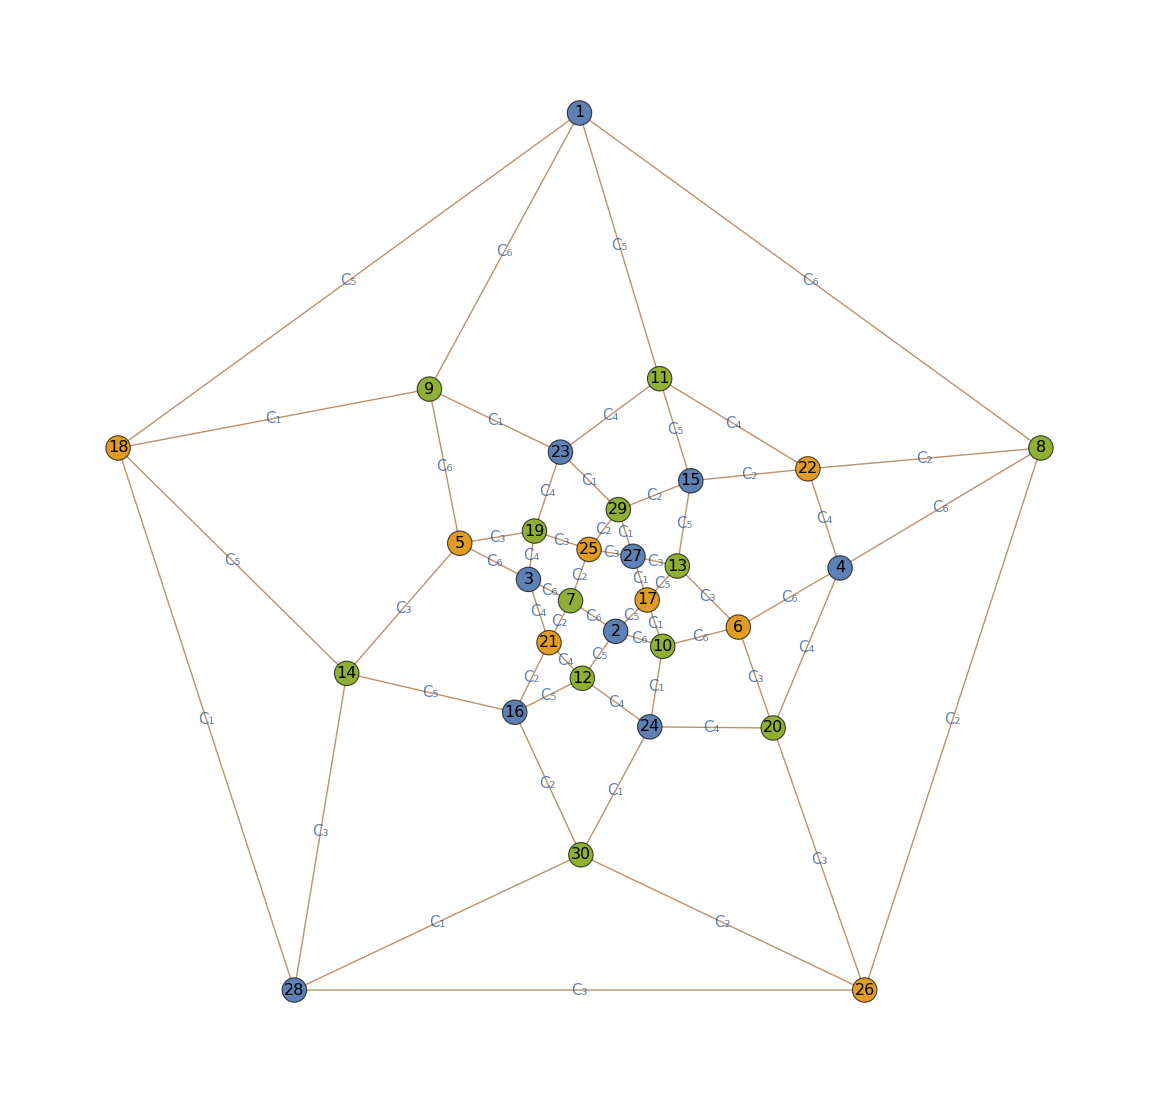

```mathematica
VERTEXSIZE=0.55;
VERTEXLABELSIZE=16; 
EDGELABELSSIZE=15;
MEvaluate["[AdjacencyMat_MATLAB, CirclesMat] = Great_Circles_Problem_3D(6); close all;"]; 

AdjacencyMat = IntegerPart[MGet["AdjacencyMat_MATLAB"]];
CirclesMat=IntegerPart[MGet["CirclesMat"]];

g=AdjacencyGraph[AdjacencyMat,GraphLayout->"TutteEmbedding",
VertexLabels->Placed["Name",{1/2,1/2}], VertexSize->VERTEXSIZE,
VertexLabelStyle->Directive[Black,VERTEXLABELSIZE],  
EdgeShapeFunction->{{Thick,Brown,Line[#1]}&}];

NUMVER=Length[CirclesMat[[1]]];

Do[If[j== NUMVER,NEXT=1,NEXT=j+1];
g=SetProperty[g,{EdgeLabels->{CirclesMat[[i,j]]<->CirclesMat[[i,NEXT]]->Style[Subscript[C, i],FontSize->EDGELABELSSIZE]}}],

{i,1,Length[CirclesMat]}, {j,1,NUMVER}];

mvc=MinimumVertexColoring@ToCombinatoricaGraph[g];

GColored1=SetProperty[g,System`VertexStyle->Thread[System`VertexList[g]->(ColorData[97]/@mvc)]]
```